## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.

```mathematica
SetDirectory[NotebookDirectory[]];
LNe1sgrid=Import["Ne_1s_grid.dat"];
LNe2sgrid=Import["Ne_2s_grid.dat"];
LNe2pxgrid=Import["Ne_2px_grid.dat"];
LNe2pygrid=Import["Ne_2py_grid.dat"];
LNe2pzgrid=Import["Ne_2pz_grid.dat"];
ResetDirectory[];

fNe1s=Interpolation[LNe1sgrid,InterpolationOrder->1]
fNe2s=Interpolation[LNe2sgrid,InterpolationOrder->1]
fNe2px=Interpolation[LNe2pxgrid,InterpolationOrder->1]
fNe2py=Interpolation[LNe2pygrid,InterpolationOrder->1]
fNe2pz=Interpolation[LNe2pzgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«2 more identical outputs»

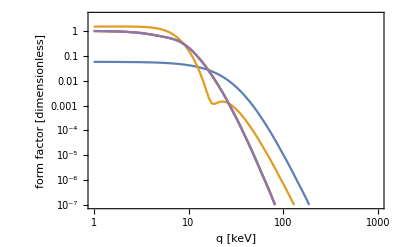

```mathematica
EtestkeV=0.025;

LogLogPlot[{fNe1s[q,EtestkeV],fNe2s[q,EtestkeV],fNe2px[q,EtestkeV],fNe2py[q,EtestkeV],fNe2pz[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

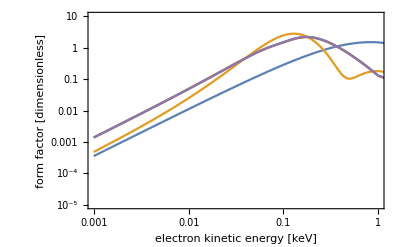

```mathematica
qtestkeV=10;

LogLogPlot[{fNe1s[qtestkeV,E1],fNe2s[qtestkeV,E1],fNe2px[qtestkeV,E1],fNe2py[qtestkeV,E1],fNe2pz[qtestkeV,E1]},{E1,0.001,1000},PlotRange->{{0.001,1},{10^-5,10}},Frame->True,FrameLabel->{"electron kinetic energy [keV]","form factor [dimensionless]"}]
```